# Naloga 1

```mathematica
Get["C:\\Users\\Admin\\Desktop\\NRO DN2\\monteMačus.m"]
```

Pribljižek vrednosti π:3.138

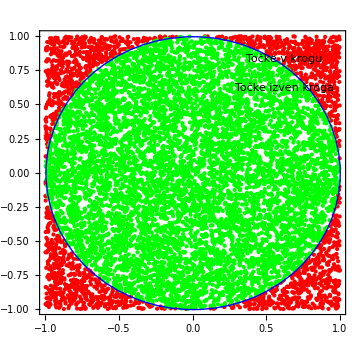

```mathematica
(*Pognati moramo datoteko monteMačus, da se funkcija kodaMonteC pravilno izvede*)
kodaMonteC[10000]
```

# Naloga 2

```mathematica
(*Določimo funkciji:*)
funkcija1=Normal[Table[Series[fun1[t],{t,2,n}],{n,0,15}]];
funkcija2[t_]=Sin[t]*t^2*Exp[-t];

(*Zapišemo kodo za grafični izris:*)
Manipulate[Plot[{funkcija2[t],funkcija1[[r]]},{t,0,4},
AxesLabel->{"t","y"},
PlotLegends->{"funkcija Sin(t)t^2 e^-t",StringForm["Taylorjeva vrsta reda ``.",r-1]}, PlotStyle->{Red,Green}, PlotTheme->"Business"],
{r,1,11,1}]
```